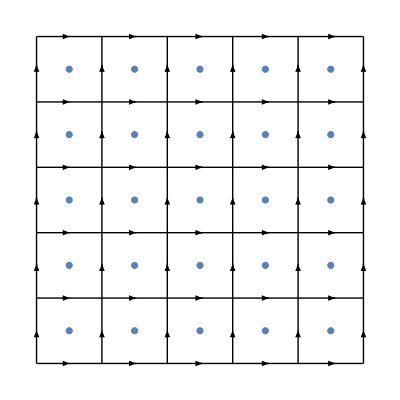

```mathematica
Xmax=1; Xmin=0; Ymax=1; Ymin=0; dx=0.2; dy = 0.2; d= 0.015;
ver[x_]:=Graphics[Line[{{x,Ymin},{x,Ymax}}]]
var[y_]:=Graphics[Line[{{Xmin,y},{Xmax,y}}]]
do[x_]:=Graphics[ListPlot[Table[{x,y},{y,Ymin+dy/2,Ymax,dy}]]]
varr[x_]:=Graphics[{Arrowheads[0.015],Table[Arrow[{{x,y},{x,(1+d)y}}],{y,Ymin + dy/2,Ymax,dy}]}]
sarr[x_]:=Graphics[{Arrowheads[0.015],Table[Arrow[{{x,y},{(1+d)x,y}}],{y,Ymin ,Ymax,dy}]}]
Show[Table[ver[x],{x,Xmin,Xmax,dx}],
Table[var[y],{y,Ymin,Ymax,dy}],
Table[do[x],{x,Xmin+dx/2,Xmax,dx}],
Table[varr[x],{x,Xmin,Xmax,dx}],
Table[sarr[x],{x,Xmin+dx/2,Xmax,dx}],
ImageSize->Full]
```